## CP-10: Graphical analysis of non-linear systems

```mathematica
Quit[]
```

## Graphical analysis of non-linear systems

For an overview of the relevant Mathematica commands, refer to chapter 12 of the tutorial, and also to chapters 9 & 10, since many commands are very similar to those used in linear systems (e.g., how to plot time and phase diagrams).

### Exercise 10-1: Morley’s catastrophe

For this exercise we analyze a functional response curve of Holling type III: ⅆN/ⅆt=r·N·(1-N/K)-P·E·N^2/(N^2+H^2)

(a) Make a time-plot for parameters r=1, K=10, E=5, H=0.5, P=0.1 and N_0=10

```mathematica
timeMorley[P_, N0_]:=Module[{r=1,K=10,E=5,H=0.5, sysN,fN, Nt, eq, maxT=50},
sysN=D[n[t],t]==r*n[t]*(1-n[t]/K)-P*E*n[t]^2/(n[t]^2+H^2);
fN=r*n*(1-n/K)-P*E*n^2/(n^2+H^2);
Nt=NDSolveValue[{sysN, n[0]==N0}, n[t],{t,0,maxT}];
eq=Values[NSolve[fN==0, n, Reals]];
Print["Equilibrium N^= ",eq];
Plot[Nt, {t, 0, maxT}, PlotLabel->"Time plot", AxesLabel->{"t", "N"}, PlotRange->{All, {0,11}}]
]
```

Equilibrium N^= {{0.},{9.47369}}

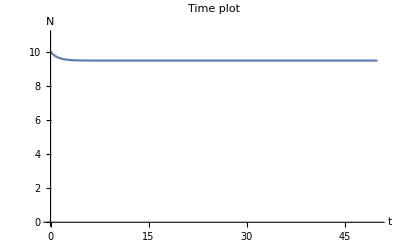

```mathematica
timeMorley[0.1,10]
```

(b) Increase P from 0.1 to 0.6 in steps of 0.1, and find the equilibrium N̂ where the system collapses.

```mathematica
Manipulate[timeMorley[parP, 10],{{parP, 0.1, "P"}, 0.1, 0.6, 0.1}]
```

Equilibrium N^= {{0.},{9.47369}}

Equilibrium N^= {{0.},{0.378106},{0.74483},{8.87706}}

Equilibrium N^= {{0.},{0.18626},{1.64263},{8.17111}}

Equilibrium N^= {{0.},{0.13194},{2.61096},{7.2571}}

Equilibrium N^= {{0.},{0.103183},{4.44054},{5.45628}}

Equilibrium N^= {{0.},{0.0850135}}

The system (population of prey) collapses when predator parameter P=0.6, which is the maximum value in the tested range. For P=0.5, 0.4, 0.3, 0.2, there are 4 equilibria. Given that the initial condition N0 is 10, and the system in all these 4 cases converge to the 4th equilibrium, those 4th equilibria are stable.

(c) Set N_0=N̂ =0.085, and decrease P from 0.6 to 0.1 in steps of 0.1. At which point will the system recover?

```mathematica
Manipulate[timeMorley[parP, 0.085],{{parP, 0.6, "P"}, 0.1, 0.6, 0.1}]
```

Equilibrium N^= {{0.},{0.0850135}}

Equilibrium N^= {{0.},{0.103183},{4.44054},{5.45628}}

Equilibrium N^= {{0.},{0.13194},{2.61096},{7.2571}}

Equilibrium N^= {{0.},{0.18626},{1.64263},{8.17111}}

Equilibrium N^= {{0.},{0.378106},{0.74483},{8.87706}}

Equilibrium N^= {{0.},{9.47369}}

Only for P=0.1, the system can converge back to 9.47 from N0=0.085, since this is the only and stable equilibrium. For P=0.2, 0.3, 0.4, 0.5, the system converged to a different equilibria (the 2nd equilibria in the result lists).

(d) Plot ⅆN/ⅆt against N for P=0.1, 0.3 and 0.6. How many equilibria do you find?

```mathematica
growthMorley[P_]:=Module[{r=1,K=10,E=5,H=0.5, fN,maxN=10},
fN=r*n*(1-n/K)-P*E*n^2/(n^2+H^2);
Plot[fN, {n, 0,maxN}, PlotLabel->"Plot of dN/dt", AxesLabel->{"N","f(N)"},AxesOrigin->{0.0,0.0}]
]
```

```mathematica
Manipulate[growthMorley[parP],{{parP, 0.1, "P"}, 0.1, 0.6, 0.1}]
```

Same things observed: Two equilibria for P=0.1 and P=0.6. While for P from 0.2 to 0.5, there are 4 equilibria.

(e) Make a “catastrophe diagram” by plotting N̂ against P.

(1-n/10) n-(5 n^2 P)/(0.25+n^2)

{(0.2 (1.-0.1 n) (0.25+n^2))/n}

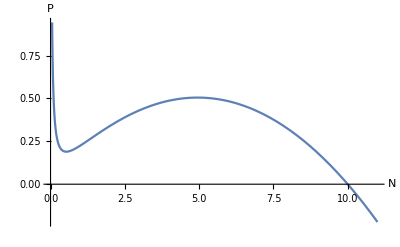

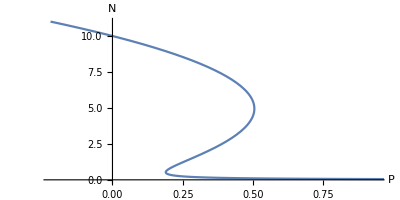

```mathematica
fN=r*n*(1-n/K)-P*E*n^2/(n^2+H^2);
rhs=fN/.{r->1,K->10,E->5,H->0.5}
eqP=NSolveValues[rhs==0,P]
Plot[eqP[[1]],{n,0,11}, AxesLabel->{"N", "P"}]
ParametricPlot[{eqP[[1]],n},{n,0,11},AspectRatio-> 1/2, AxesLabel->{"P", "N"}]
```

### Exercise 10-2: The Rosenzweig-McArthur model

For this exercise we consider the Rosenzweig-McArthur model with type III functional response: ⅆR/ⅆt=r·R·(1-R/K)-(b·R^2N)/(h^2+R^2), ⅆN/ⅆt=(c·b·N·R^2)/(h^2+R^2)-d·N, with parameters r=1, b=1,c=4, h=16.

(a) Draw the time plots for various values of d (between 1 and 3.99) and K (between 1 and 500).

```mathematica
timeArthur[d_,k_, R0_, N0_, maxT_]:=Module[{r=1, b=1, c=4, h=16, eqR, eqN, rhsR, rhsN,sol},
eqR=D[R[t],t]==r*R[t]*(1-R[t]/k)-(b*R[t]^2*n[t])/(h^2+R[t]^2);
eqN=D[n[t],t]==c*b*n[t]*R[t]^2/(h^2+R[t]^2)-d*n[t];
rhsR=r*R*(1-R/k)-(b*R^2*n)/(h^2+R^2);
rhsN=c*b*n*R^2/(h^2+R^2)-d*n;
sol=NDSolveValue[{eqR, eqN, R[0]==R0, n[0]==N0},{R[t],n[t]},{t, 0,maxT}];
Plot[sol,{t,0,maxT},PlotLabel->"Time plot Rosenzweig-McArthur model", AxesLabel->{"t", "R, N"}]
]
```

```mathematica
Manipulate[timeArthur[d, k, r0, n0, 100],{{d, 1, "d"}, 1, 3.99}, {{k, 1, "k"}, 1, 500}, {{r0, 20, "R[0]"}, 0.1, 50}, {{n0, 20, "N[0]"}, 0.1, 50}]
```

For small d, K can be extensively large without destabilizing the system. As d increases, increase in K destabilize the system and decrease in K stabilize the system.
In sum, decreasing d and decreasing K have stabilize effects.

(b) Now assume K=130. Draw the null clines in a phase plane plot and look how the null clines change for different values of d.

```mathematica
r=1;b=1;c=4;h=16;
rhsR=r*R*(1-R/k)-(b*R^2*n)/(h^2+R^2);
rhsN=c*b*n*R^2/(h^2+R^2)-d*n;
SolveValues[rhsR==0,R]
SolveValues[rhsR==0,n]
SolveValues[rhsN==0,R]
SolveValues[rhsN==0,n]
```

{0,k/3+(2^(1/3) (768-k^2+3 k n))/(3 (-4608 k-2 k^3+9 k^2 n+√(4 (768-k^2+3 k n)^3+(-4608 k-2 k^3+9 k^2 n)^2))^(1/3))-((-4608 k-2 k^3+9 k^2 n+√(4 (768-k^2+3 k n)^3+(-4608 k-2 k^3+9 k^2 n)^2))^(1/3))/(3 2^(1/3)),k/3-((1+ⅈ √3) (768-k^2+3 k n))/(3 2^(2/3) (-4608 k-2 k^3+9 k^2 n+√(4 (768-k^2+3 k n)^3+(-4608 k-2 k^3+9 k^2 n)^2))^(1/3))+((1-ⅈ √3) (-4608 k-2 k^3+9 k^2 n+√(4 (768-k^2+3 k n)^3+(-4608 k-2 k^3+9 k^2 n)^2))^(1/3))/(6 2^(1/3)),k/3-((1-ⅈ √3) (768-k^2+3 k n))/(3 2^(2/3) (-4608 k-2 k^3+9 k^2 n+√(4 (768-k^2+3 k n)^3+(-4608 k-2 k^3+9 k^2 n)^2))^(1/3))+((1+ⅈ √3) (-4608 k-2 k^3+9 k^2 n+√(4 (768-k^2+3 k n)^3+(-4608 k-2 k^3+9 k^2 n)^2))^(1/3))/(6 2^(1/3))}

{((k-R) (256+R^2))/(k R)}

{-(16 √d)/(√(4-d)),(16 √d)/(√(4-d))}

{0}

```mathematica
isocline[d_,k_]:=Module[{r=1, b=1, c=4, h=16, eqR, eqN, rhsR, rhsN,isoR, isoN, plotIR, plotIN},
eqR=D[R[t],t]==r*R[t]*(1-R[t]/k)-(b*R[t]^2*n[t])/(h^2+R[t]^2);
eqN=D[n[t],t]==c*b*n[t]*R[t]^2/(h^2+R[t]^2)-d*n[t];
rhsR=r*R*(1-R/k)-(b*R^2*n)/(h^2+R^2);
rhsN=c*b*n*R^2/(h^2+R^2)-d*n;
isoR=SolveValues[rhsR==0,n];
isoN=SolveValues[rhsN==0,R];(*derive 2 solutions, but the 1st solution gives negative R (for positive d, see above), which is not biologically meaningful*)
plotIR=Plot[isoR,{R, 0, 100}, AxesLabel->{"R", "N"}, PlotStyle->Blue,PlotRange->{{0,100}, {0,100}}];
plotIN=ParametricPlot[{isoN[[2]], n}, {n, 0, 100}, AxesLabel->{"R", "N"}, PlotStyle->Red, PlotRange->{{0,100}, {0,100}}];
Show[plotIR, plotIN]
]
```

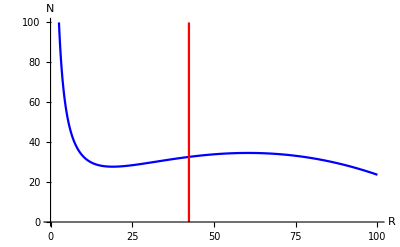

```mathematica
isocline[3.5,130]
```

```mathematica
Manipulate[isocline[d,130],{{d, 1,"d"},1,3.99,0.1}]
```

Changing d would shift the isocline dN/dt=0 to the right-hand side. Therefore, the slope at the intersection of the two isoclines, i.e. the equilibrium, would change accordingly. Here, I also see that changing d only change the isocline of N, but not the isocline of R. Since as can be seen above, the isocline of R only depends on K, while the isocline of N only depends on d.

```mathematica
Manipulate[isocline[d,k],{{d, 1,"d"},1,3.99,0.1}, {{k, 1, "k"}, 1, 500}]
```

When the null cline of R has one local minimum for small R and one local maximum for large R. The equilibrium is unstable when the isocline of N lies between those two local extrema. Because the equilibrium is the intersect between the 2 isoclines and it is unstable when the slope of the isocline of R at that point is >0.

(c) Determine the stability of the intersection point of the two null clines (i.e., the equilibrium) for the different values of d.

```mathematica
eigenArthur[d_,k_]:=Module[{r=1, b=1, c=4, h=16, eqR, eqN, rhsR, rhsN,isoR, isoN, eqPoint, j},
eqR=D[R[t],t]==r*R[t]*(1-R[t]/k)-(b*R[t]^2*n[t])/(h^2+R[t]^2);
eqN=D[n[t],t]==c*b*n[t]*R[t]^2/(h^2+R[t]^2)-d*n[t];
rhsR=r*R*(1-R/k)-(b*R^2*n)/(h^2+R^2);
rhsN=c*b*n*R^2/(h^2+R^2)-d*n;
isoR=SolveValues[rhsR==0,n];
isoN=SolveValues[rhsN==0,R];(*derive 2 solutions, but the 1st solution gives negative R (for positive d, see above), which is not biologically meaningful*)

eqPoint={isoN[[2]], isoR[[1]]/.R->isoN[[2]]}; (*equilibrium is the intersect of 2 null clines*)
j=D[{rhsR, rhsN}, {{R, n}}]/.{R->eqPoint[[1]], n->eqPoint[[2]]};
Re[Eigenvalues[j]]
]
```

```mathematica
eigenArthur[3.5,130]
```

{0.0900729,0.0900729}

```mathematica
Manipulate[eigenArthur[d,k],{{d, 1,"d"},1,3.99,0.1}, {{k, 1, "k"}, 1, 500}]
```

(d) Draw the solution of the system of ODEs from (a) in the phase plane plot and look at how it changes as d  changes from 1 to 3.99.

```mathematica
phaseArthur[d_,k_, R0_, N0_, maxT_]:=Module[{r=1, b=1, c=4, h=16, eqR, eqN, rhsR, rhsN,sol, phase, isoR, isoN, plotIR, plotIN, field},
eqR=D[R[t],t]==r*R[t]*(1-R[t]/k)-(b*R[t]^2*n[t])/(h^2+R[t]^2);
eqN=D[n[t],t]==c*b*n[t]*R[t]^2/(h^2+R[t]^2)-d*n[t];
rhsR=r*R*(1-R/k)-(b*R^2*n)/(h^2+R^2);
rhsN=c*b*n*R^2/(h^2+R^2)-d*n;

sol=NDSolveValue[{eqR, eqN, R[0]==R0, n[0]==N0},{R[t],n[t]},{t, 0,maxT}];
phase=ParametricPlot[sol,{t,0,maxT},PlotLabel->"Phase plot Rosenzweig-McArthur model", AxesLabel->{"R", "N"},PlotStyle->{RGBColor["#32a47d"], Thickness[0.005]}, PlotRange->{{0,300},{0,300}}];

isoR=SolveValues[rhsR==0,n];
isoN=SolveValues[rhsN==0,R];(*derive 2 solutions, but the 1st solution gives negative R (for positive d, see above), which is not biologically meaningful*)
plotIR=Plot[isoR,{R, 0, 300}, AxesLabel->{"R", "N"}, PlotStyle->Blue];
plotIN=ParametricPlot[{isoN[[2]], n}, {n, 0, 300}, AxesLabel->{"R", "N"}, PlotStyle->Red];

field=StreamPlot [{rhsR,rhsN},{R,0,300},{n,0,300},StreamScale->{Tiny,Automatic,0.01}, StreamColorFunction->None, StreamStyle->Gray];

Show[{phase,plotIR,plotIN,field},AspectRatio->1,AxesLabel->{"R","N"}, ImageSize->{600,600}]
]
```

```mathematica
Manipulate[phaseArthur[d,k,100,100,100],{{d, 1,"d"},1,3.99,0.1}, {{k, 1, "k"}, 1, 500}]
```

At d=2.4 and K=157, the system first approaches the equilibrium, but it can never converge to the equilibrium. Looking at the vector field at the equilibrium shows that the stream runs away from the equilibrium. Possibly, this is a saddle point. I predict that the system has two eigenvalues in which one has negative real part and other has positive real part.

```mathematica
eigenArthur[2.4,157]
```

{0.0251111,0.0251111}

Oh, my prediction was wrong! Why? Probably because looking at the eigenvalues of the Jacobian matrix can only tell us about the local behaviour near the equilibrium but not the global behaviour!

```mathematica
eigenArthur[2.4,140]
```

{0.0160175,0.0160175}

Limit cycle is observed at d=2.4 and K=140, the system oscillates around the equilibrium but can never reach there.
Limit cycle comes from unstable equilibrium.